```mathematica
Clear["Global`*"]
```

```mathematica
delta={2.44,2.54,2.64,2.74,2.84,2.94,3.04,3.14,3.24,3.34,3.44,3.54,3.64};
```

```mathematica
eigen2by2b16n115={0.386368588,0.400754569,0.417874367,0.433126755,0.459750229,0.467265408,0.479788873,0.483427915,0.492421365,0.494657919,0.499726385,0.494997745,0.489602117};
```

```mathematica
eigen2by2b32n115={0.652737408,0.683950561,0.720002472,0.745000372,0.765166809,0.781272296,0.788323779,0.804225071,0.806952243,0.802801842,0.809444898,0.798215898,0.792424736};
```

```mathematica
eigen2by2b40n115={0.77614791,0.800216685,0.829871779,0.849157,0.864491686,0.889333287,0.890463833,0.899920694,0.899243286,0.895096904,0.899170189,0.890607505,0.888221819};
```

```mathematica
eigen2by2b50n115={0.89881,0.92755,0.94337,0.96846,0.97477097,0.97923,0.990158157,0.989706802,0.98263,0.9763461372273271,0.97377,0.96437,0.94867};
```

```mathematica
eigen2by2b56n115={0.95223,0.96943,0.98775,1.001456075,1.00411,1.01265,1.02021,1.00149,1.00768,0.99556,0.97960,0.98388,0.96237};
```

```mathematica
eigen2by2b64n115={0.98525,1.00014,1.00824,1.02406,1.01820,1.02281,1.02777,1.0082,0.99490,0.97982,0.97577,0.95912,0.93980};
```

```mathematica
eigen2by2d234={{1/50,0.86441},{1/56,0.91670},{1/64,0.96701},{1/72,0.934868957}};
```

```mathematica
eigen2by2d244={{1/40,0.77614791},{1/50,0.89881},{1/56,0.95223},{1/64,0.98525},{1/72,0.968578898}};
```

```mathematica
eigen2by2d254={{1/40,0.800216685},{1/50,0.92755},{1/56,0.96943},{1/64,1.00014}};
```

```mathematica
eigen2by2d264={{1/40,0.829871779},{1/50,0.94337},{1/56,0.98775},{1/64,1.00824}};
```

```mathematica
eigen2by2d274={{1/40,0.849157},{1/50,0.96846},{1/56,1.001456075}};
```

```mathematica
eigen2by2d284={{1/40,0.864491686},{1/50,0.97477097},{1/56,1.00411},{1/64,1.01820}};
```

```mathematica
feigen2by2d234=SplineFit[eigen2by2d234,Cubic];
```

```mathematica
figeigen2by2d234=ParametricPlot[Evaluate[Through[{feigen2by2d234}[t]]],{t,0,3},PlotStyle->RGBColor[0.915, 0.3325, 0.2125]];
```

```mathematica
feigen2by2d244=SplineFit[eigen2by2d244,Cubic];
```

```mathematica
figeigen2by2d244=ParametricPlot[Evaluate[Through[{feigen2by2d244}[t]]],{t,0,4},PlotStyle->RGBColor[0.40082222609352647, 0.5220066643438841, 0.85]];
```

```mathematica
feigen2by2d254=SplineFit[eigen2by2d254,Cubic];
```

```mathematica
figeigen2by2d254=ParametricPlot[Evaluate[Through[{feigen2by2d254}[t]]],{t,0,4},PlotStyle->  RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142]];
```

```mathematica
feigen2by2d264=SplineFit[eigen2by2d264,Cubic];
```

```mathematica
figeigen2by2d264=ParametricPlot[Evaluate[Through[{feigen2by2d264}[t]]],{t,0,4},PlotStyle->  RGBColor[0.736782672705901, 0.358, 0.5030266573755369]];
```

```mathematica
feigen2by2d274=SplineFit[eigen2by2d274,Cubic];
```

```mathematica
figeigen2by2d274=ParametricPlot[Evaluate[Through[{feigen2by2d274}[t]]],{t,0,4},PlotStyle->  RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]];
```

```mathematica
Linepoints={{0.01,1.0},{0.024,1}};
```

```mathematica
line=ListPlot[Linepoints,Joined->True, PlotStyle->{Dashed,Black}];
```

```mathematica
AA=ListPlot[{eigen2by2d234,eigen2by2d244,eigen2by2d254,eigen2by2d264,eigen2by2d274},PlotRange->{{0.012,0.026},Automatic},PlotMarkers->{Automatic,10},PlotStyle->{RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},PlotLegends->Placed[LineLegend[{"Δ = 2.34","Δ = 2.44","Δ = 2.54","Δ = 2.64","Δ = 2.74"},LabelStyle->{14},LegendLayout->{"Row",2}],{0.41,0.13}],Frame->True,FrameTicks->{{Automatic,Automatic},{{0.013,0.017,0.021,0.025},Automatic}},AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"T (eV)","λ_d"}];
```

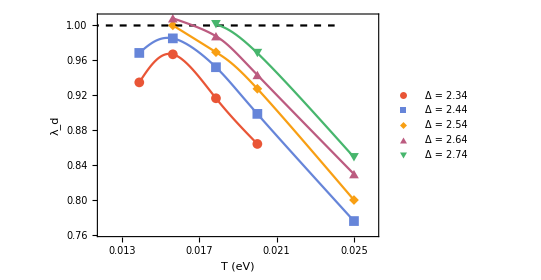

```mathematica
eigen2by2n115vsTvarydelta1=Show[AA,line,figeigen2by2d234,figeigen2by2d244,figeigen2by2d254,figeigen2by2d264,figeigen2by2d274]
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/MS_pairing_correlation/eigen2by2n115vsTvarydelta1.pdf",eigen2by2n115vsTvarydelta1,"PDF"];
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
eigen2by2d314={{1/40,0.894989164},{1/50,0.989706802},{1/56,1.00149}};
```

```mathematica
eigen2by2d324={{1/40,0.899243286},{1/50,0.98263},{1/56,1.00768}};
```

```mathematica
eigen2by2d334={{1/40,0.895096904},{1/50,0.976346137},{1/56,0.99556}};
```

```mathematica
eigen2by2d344={{1/40,0.899170189},{1/50,0.97377},{1/56,0.97960},{1/64,0.97577},{1/72,0.940701819}};
```

```mathematica
eigen2by2d354={{1/40,0.890607505},{1/50,0.96437},{1/56,0.98388},{1/64,0.95912}};
```

```mathematica
eigen2by2d364={{1/40,0.888221819},{1/50,0.94867},{1/56,0.96237},{1/64,0.93980}};
```

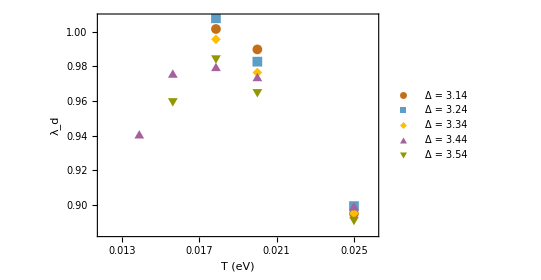

```mathematica
BB=ListPlot[{eigen2by2d314,eigen2by2d324,eigen2by2d334,eigen2by2d344,eigen2by2d354},PlotRange->{{0.012,0.026},Automatic},PlotMarkers->{Automatic,10},PlotStyle->{RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]},PlotLegends->Placed[LineLegend[{"Δ = 3.14","Δ = 3.24","Δ = 3.34","Δ = 3.44","Δ = 3.54"},LabelStyle->{14},LegendLayout->{"Row",2}],{0.41,0.13}],Frame->True,FrameTicks->{{Automatic,Automatic},{{0.013,0.017,0.021,0.025},Automatic}},AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"T (eV)","λ_d"}]
```

```mathematica
eigen2by2d314
```

{{1/40,0.894989},{1/50,0.989707},{1/56,1.00149}}

```mathematica
nlm=NonlinearModelFit[eigen2by2d314,a+b*x+c*x^2,{a,b,c},x]
```

FittedModel[0.427448+65.7581 x-1882.26 x^2]

```mathematica
figeigen2by2d314=Plot[nlm[x],{x,1/56,1/40},PlotStyle->  RGBColor[0.772079, 0.431554, 0.102387]];
```

```mathematica
eigen2by2d324
```

{{1/40,0.899243},{1/50,0.98263},{1/56,1.00768}}

```mathematica
nlm=NonlinearModelFit[eigen2by2d324,a+b*x+c*x^2,{a,b,c,d},x]
```

FittedModel[0.967063+14.7429 x-698.228 x^2]

```mathematica
figeigen2by2d324=Plot[nlm[x],{x,1/56,1/40},PlotStyle->  RGBColor[0.363898, 0.618501, 0.782349]];
```

```mathematica
eigen2by2d334
```

{{1/40,0.895097},{1/50,0.976346},{1/56,0.99556}}

```mathematica
nlm=NonlinearModelFit[eigen2by2d334,a+b*x+c*x^2,{a,b,c,d},x]
```

FittedModel[0.791507+29.6354 x-1019.67 x^2]

```mathematica
figeigen2by2d334=Plot[nlm[x],{x,1/56,1/40},PlotStyle->  RGBColor[1, 0.75, 0]];
```

```mathematica
eigen2by2d344
```

{{1/40,0.89917},{1/50,0.97377},{1/56,0.9796},{1/64,0.97577},{1/72,0.940702}}

```mathematica
nlm=NonlinearModelFit[eigen2by2d344,a+b*x+c*x^2+d*x^3,{a,b,c,d},x]
```

FittedModel[-0.458348+201.277 x-8926.26 x^2+121898. x^3]

```mathematica
figeigen2by2d344=Plot[nlm[x],{x,1/72,1/40},PlotStyle->  RGBColor[0.647624, 0.37816, 0.614037]];
```

```mathematica
eigen2by2d354
```

{{1/40,0.890608},{1/50,0.96437},{1/56,0.98388},{1/64,0.95912}}

```mathematica
nlm=NonlinearModelFit[{{1/40,0.890607505},{1/50,0.96437},{1/56,0.98388}},a+b*x+c*x^2,{a,b,c},x]
```

FittedModel[0.864072+20.8288 x-790.697 x^2]

```mathematica
figeigen2by2d3540=Plot[nlm[x],{x,1/56,1/40},PlotStyle->  RGBColor[0.571589, 0.586483, 0.]];
```

```mathematica
nlm=NonlinearModelFit[{{1/50,0.96437},{1/56,0.98388},{1/64,0.95912}},a+b*x+c*x^2,{a,b,c},x]
```

FittedModel[-0.502283+165.662 x-4616.49 x^2]

```mathematica
figeigen2by2d3541=Plot[nlm[x],{x,1/64,1/56},PlotStyle->  RGBColor[0.571589, 0.586483, 0.]];
```

```mathematica
feigen2by2d354=SplineFit[eigen2by2d354,Cubic];
```

```mathematica
figeigen2by2d354=ParametricPlot[Evaluate[Through[{feigen2by2d354}[t]]],{t,0,3},PlotStyle->  RGBColor[0.571589, 0.586483, 0.]];
```

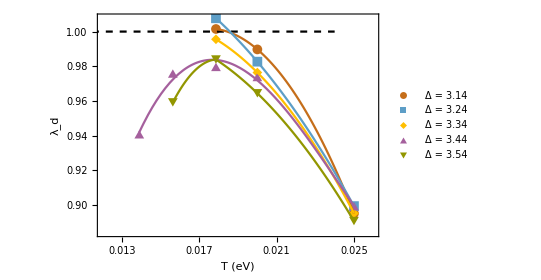

```mathematica
eigen2by2n115vsTvarydelta2=Show[BB,line,figeigen2by2d314,figeigen2by2d324,figeigen2by2d334,figeigen2by2d344,figeigen2by2d3540,figeigen2by2d3541]
```